# House-of-cards approximation for ancestral equilibrium

## attempt #1

First define the mutational kernel g and fitness function w (here in 2-dimensions):

```mathematica
g[x1_,x2_]:=(ⅇ^(1/2 (-x1^2/λ-x2^2/λ)))/(2 π λ)
w[x1_,x2_]:=ⅇ^(1/2 (-x1^2-x2^2))
```

where λ is the variance in mutational effect in each dimension and x1 and x2 are the trait values in each dimension.

Then at equilibrium, under the house-of-cards (HoC) approximation, the distribution of trait values is (Turelli 1984 eqn 3.2a)

```mathematica
p[x1,x2]==(μ g[x1,x2])/(1-k w[x1,x2])/.k->(1-μ)/Integrate[p[x1,x2]w[x1,x2],{x1,-∞,∞},{x2,-∞,∞}];
sol=Simplify[Solve[{%},p[x1,x2]],λ>0]
FullSimplify[%%/.%[[2]],{λ>0,1≥μ>0}]
%/.μ->0.001/.λ->0.005/.x1->1/.x2->2
```

{{p[x1,x2]→0},{p[x1,x2]→(ⅇ^(-((x1^2+x2^2) (1+λ))/(2 λ)) (-ⅇ^((x1^2+x2^2)/(2 λ)) λ (-1+μ)+ⅇ^(1/2 (x1^2+x2^2)) μ))/(2 π λ)}}

((-1+μ) (ⅇ^(((x1^2+x2^2) (1+λ))/(2 λ)) λ (-1+λ (-1+μ)-μ)+2 (1+λ) (-ⅇ^((x1^2+x2^2)/(2 λ)) λ (-1+μ)+ⅇ^(1/2 (x1^2+x2^2)) μ)))/(ⅇ^(1/2 (x1^2+x2^2)) (-1+λ (-1+μ)-μ)-2 (1+λ) (-1+μ))==0

False

[mathematica is not finding the right solution]

Note that HoC requires the variance of new mutations to be much greater than that which exists (in our case in each dimension): λ>>V_g (Turelli 1984 eqn 2.29).

Plot this equilibrium HoC distribution

```mathematica
p[x1,x2]/.sol[[2]]/.λ->0.005/.μ->0.0001;
Plot3D[%,{x1,-3,3},{x2,-3,3},PlotRange->{0,0.2}]
```

-Graphics3D-

Check that the solution is good (trait distribution integrates to 1)

```mathematica
Integrate[p[x1,x2]/.sol,{x1,-∞,∞},{x2,-∞,∞},Assumptions->λ>0]
```

{0,1}

What is mean fitness at equilibrium?

```mathematica
Simplify[Integrate[p[x1,x2]w[x1,x2],{x1,-∞,∞},{x2,-∞,∞}]/.sol[[2]],λ>0]
%/.λ->0.005/.μ->0.0001
```

(1+λ+μ-λ μ)/(2+2 λ)

0.50005

weird??! way too low

Convert from trait to fitness, to plot equilibrium fitness distribution

{{x1→-√(-x2^2+2 Log[1/W])},{x1→√(-x2^2+2 Log[1/W])}}

{(W λ+W^(1/λ) μ-W λ μ)/(2 π λ),(W λ+W^(1/λ) μ-W λ μ)/(2 π λ)}

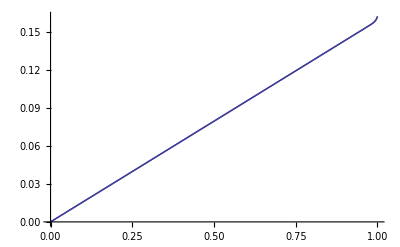

```mathematica
Solve[w[x1,x2]==W,x1]/.C[1]->0
Simplify[p[x1,x2]/.sol[[2]]/.%,{W>0,λ>0}]
Plot[%/.λ->0.005/.μ->0.0001,{W,0,1},PlotRange->All]
```

this gotta be wrong!

## attempt #2

Lets go straight to fitness.

We start with Martin & Lenormand’s (2016) PDF of selective effects

```mathematica
fs[s_,so_,λ_,n_]:=2/λ PDF[NoncentralChiSquareDistribution[n,(2so)/λ],2/λ(so-s)]HeavisideTheta[so-s];
```

where so = m_max-m_wt is the selection coefficient of the optimum phenotype, λ is the mutational variance per trait, and n is the number of traits under selection.

In our case we will have so=0, giving us a gamma distribution (see Martin & Lenormand 2006)

-(ⅇ^(s/λ) (-s/λ)^(n/2))/(s Gamma[n/2])

True

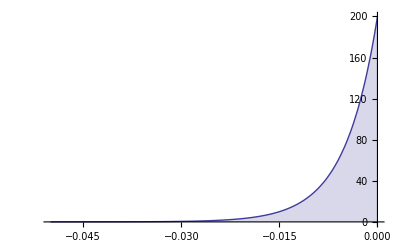

```mathematica
Simplify[fs[s,0,λ,n],{s<0,λ>0}]
%==Simplify[PDF[GammaDistribution[n/2,λ],-s],{s<0,λ>0}]
Plot[%%/.λ->0.005/.n->2,{s,-0.05,0},PlotRange->All,Filling->0]
```

Shift this to be the distribution of fitness

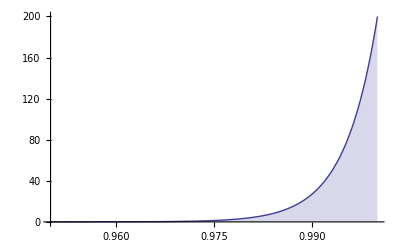

```mathematica
g[W_]:=Simplify[PDF[TransformedDistribution[1-s,s\[Distributed]GammaDistribution[n/2,λ]],W],{W<1,λ>0}]
Plot[g[W]/.λ->0.005/.n->2,{W,0.95,1},PlotRange->All,Filling->0]
```

Then at equilibrium, under the house-of-cards (HoC) approximation, the distribution of fitness is (Turelli 1984 eqn 3.2a)

```mathematica
p[W]==μ g[W]+(1-μ) W/Integrate[p[W]W,{W,0,1}] p[W]
sol=Solve[%,p[W]]

Simplify[%%/.%,{λ>0,n>0}]
Simplify[%/.μ->0.001/.n->2/.λ->0.005,1≥ W≥0]
```

p[W]==(ⅇ^((-1+W)/λ) (1-W)^(-1+n/2) λ^(-n/2) μ)/Gamma[n/2]+(W (1-μ) p[W])/(∫_0^1 W p[W]ⅆW)

{{p[W]→(-ⅇ^(-1/λ+W/λ) (1-W)^(n/2) λ^(-n/2) μ-2 W Gamma[n/2]+2 W^2 Gamma[n/2]+2 W μ Gamma[n/2]-2 W^2 μ Gamma[n/2])/(-Gamma[n/2]+W Gamma[n/2])}}

{(W (-1+μ) (ⅇ^(1/λ) (-1+W) λ^(n/2) (4+6 W (-1+μ)+(2-3 n λ) μ) Gamma[n/2]+3 μ (ⅇ^(W/λ) (1-W)^(n/2)-2 ⅇ^(1/λ) (-1+W) λ^(n/2) Gamma[n/2,1/λ]+2 ⅇ^(1/λ) (-1+W) λ^(1+n/2) Gamma[(2+n)/2,1/λ])))/((-1+W) ((-4+(-2+3 n λ) μ) Gamma[n/2]+6 μ (Gamma[n/2,1/λ]-λ Gamma[(2+n)/2,1/λ])))==0}

{-1/(-1.+W)5.40598×10^84 W (0.667663+ⅇ^(200. W) (-1.38528×10^-88+1.38528×10^-88 W)-1.66766 W+1. W^2)==0}

```mathematica
sol=Simplify[Solve[{p[W]==(μ g[W])/(1-k W)}/.k->(1-μ)/Integrate[p[W]W,{W,0,1}],p[W]],λ>0]
```

{{p[W]→0},{p[W]→(ⅇ^(-1/λ) λ^(-n/2) (-ⅇ^(W/λ) (1-W)^(n/2) μ-2 ⅇ^(1/λ) (-1+W) W λ^(n/2) (-1+μ) Gamma[n/2]))/((-1+W) Gamma[n/2])}}

```mathematica
(μ g[W])/(1-k W)/.k->Exp[-μ^2 π Vs/m^2]
%/.λ->0.005/.n->2/.μ->0.0001
(*Plot[,{W,0,1}]*)
```

(ⅇ^((-1+W)/λ) (1-W)^(-1+n/2) λ^(-n/2) μ)/((1-ⅇ^(-(π Vs μ^2)/m^2) W) Gamma[n/2])

(0.02 ⅇ^(200. (-1+W)))/(1-ⅇ^(-(3.14159×10^-8 Vs)/m^2) W)

Note that HoC requires the variance of new mutations to be much greater than that which exists (Turelli 1984 eqn 2.29).

Plot this equilibrium HoC distribution

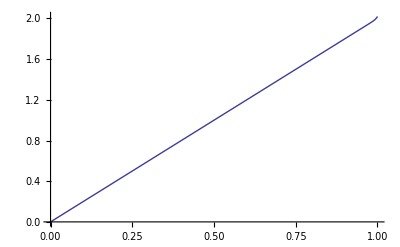

```mathematica
p[W]/.sol/.λ->0.005/.μ->0.0001/.n->2;
Plot[%,{W,0,1}]
```

again this weird linear thing

Check that the solution is good (trait distribution integrates to 1)

```mathematica
Integrate[p[W]/.sol,{W,0,1},Assumptions->{λ>0,n>0}]
%/.μ->0.0001/.n->2/.λ->0.005
```

{0,1-(μ Gamma[n/2,1/λ])/Gamma[n/2]}

{0,1.}

What is mean fitness at equilibrium?

```mathematica
Simplify[Integrate[p[W]W/.sol,{W,0,1}],{λ>0,n>0}]
%/.λ->0.005/.μ->0.0001/.n->2
```

{0,((4+(2-3 n λ) μ) Gamma[n/2]-6 μ (Gamma[n/2,1/λ]-λ Gamma[(2+n)/2,1/λ]))/(6 Gamma[n/2])}

{0,0.6667}

seems way too low